```mathematica
inGroupsOf[n_][lst_]:=Partition[lst,n,n,{1,1},{}];

quarkContent[h_,iso3_]:=
Block[{s=strangeness[h]},
Piecewise[{
{Piecewise[{
{222,iso3==3/2},{221,iso3==1/2},{211,iso3==-1/2},{111,iso3==-3/2},
{21,iso3==1||iso3==-1},{11,iso3==0}
}],s==0},
{Piecewise[{
{322,iso3==1},{321,iso3==0},{311,iso3==-1},
{32,iso3==1/2},{31,iso3==-1/2}
}],s==1},
{Piecewise[{
{332,iso3==1/2},{331,iso3==-1/2}
}],s==2}
}]
];
idCode[h_,iso3_]:=
If[Mod[idMask[h],10000]≥10,idMask[h] (* If mask specifies the number completely *), 
(idMask[h]+10quarkContent[h,iso3])*If[isMeson[h]&&iso3<0,-1,1]];
writeInterpolationData[stream_,data_]:=Module[{lines},
lines=If[#>1.*^-5,#,0.]&/@data;
lines=StringRiffle/@inGroupsOf[9][ToString/@(NumberForm[#,{6,5}]&/@lines)];
WriteString[stream,#<>"\n"]&/@lines;
];

getSpeciedProducts[h_,iso3_]:=Flatten[Table[
Block[{
outA=channel[[1,1]],outB=channel[[1,2]],br=channel[[2]],lType=2channel[[3]]+1},
Block[{
mMin=Max[-isoSpin[outA],iso3-isoSpin[outB] ],
mMax=Min[isoSpin[outA],iso3+isoSpin[outB] ]
},
Table[{{outA,iso3A},{outB,iso3-iso3A},lType},
{iso3A,mMin,mMax}]
]
],
{channel,decays[h]}
],1];

writeResonance[h_,iso3_,stream_,precision_]:=Module[{lBound,rBound,dm,speciesProducts,gammaTotal,gammas,header,lines,id},
lBound=minMass[h];
rBound=maxMass[h];
dm=(rBound-lBound)/precision;

id=idCode[h,iso3];

speciesProducts=getSpeciedProducts[h,iso3];
(* Each entry of gammas corresponds to data for one decay channel *)
gammas=Table[
Block[{
outA=channel[[1]],outB=channel[[2]],lType=channel[[3]]},
Block[{
cg=ClebschGordan[{isoSpin@outA[[1]],outA[[2]]},{isoSpin@outB[[1]],outB[[2]]},{isoSpin[h],iso3}],
mult=If[TrueQ[outA[[1]]==outB[[1]]]&&outA[[2]]≠outB[[2]],2,1]
},
Table[mult Γ[h,{outA[[1]],outB[[1]]},m] cg^2,{m,lBound,rBound,dm}]
]],
{channel,speciesProducts}
];
gammaTotal=Total[gammas]; (* Total width for particle *)
gammas = gammas/Table[gammaTotal/.{a_/;TrueQ[a==0]->Infinity},Length[gammas]];

(* Write total Gamma *)
header=StringTemplate["<width id=\"`1`\" left=\"`2`\" right=\"`3`\" mPeak=\"`4`\" data=\"\n"][id,lBound,rBound,mCenter@h];
WriteString[stream, header];
writeInterpolationData[stream,gammaTotal];
WriteString[stream,"\"/>\n\n"];

Table[
Block[{
outA=prodGammas[[1,1]],outB=prodGammas[[1,2]],lType=prodGammas[[1,3]]
},
Module[{hA,hB,iso3A,iso3B},
hA=outA[[1]];hB=outB[[1]];
iso3A=outA[[2]];iso3B=outB[[2]];
header=StringTemplate["<br id=\"`1`\" products=\"`2` `3`\" lType=\"`4`\" data=\"\n"][id,idCode[hA,iso3A],idCode[hB,iso3B],lType];
WriteString[stream,header];
writeInterpolationData[stream,prodGammas[[2]]];
WriteString[stream,"\"/>\n\n"];
]],
{prodGammas,Transpose[{speciesProducts,gammas}]}
];
WriteString[stream,"\n\n"];
];


(* Write everything to a single xml *)
writeAllResonances[precision_:100.]:=
Module[{stream,entries,iso3},
CheckAbort[
stream=OpenWrite[atNotebook["ParticleWidths 2.xml"]];
If[FailureQ[stream],Return["Failed to open stream"]];
WriteString[stream,"\n\n"];
entries=pythiaEntries[[First@First@Position[pythiaEntries,D1920] ;; ]];
Print[entries];

Monitor[
Table[
For[iso3=isoSpin[h],iso3≥-isoSpin[h],iso3--,
writeResonance[h,iso3,stream,precision]
],
{h,entries}
],
{{h,iso3},ProgressIndicator[m,{minMass@h,maxMass@h}]}
];
Close[stream];
,
Close[stream];
]
];
```

```mathematica
writeAllResonances[50.]
```

{D1920,D1950,L1405,L1520,L1600,L1670,L1690,L1690,L1800,L1810,L1820,L1830,L1890,L2100,L2110,S1385,S1660,S1670,S1750,S1775,S1915,S1940,S2030,X1530,X1820,rho,f0500,f21270}

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

```mathematica
Close@Streams[][[3]]
```

/home/b2/marius/Documents/Pythia8/Mathematica/ParticleWidths 2.xml

```mathematica
mCenter@D1920
```

$Aborted

```mathematica
Γ[D1920, {N938, pi}, minMass@D1920 + 2(maxMass@D1920 - minMass@D1920) / 10.]
```

0.0782466

```mathematica
Monitor[
Table[Γ[D1920,m],{m,minMass@D1920,maxMass@D1920,(maxMass@D1920-minMass@D1920)/10.}],
m]
```

{0.,0.147521,1.68358,2.19766,2.40456,2.52478,2.60368,2.65897,2.69944,2.72985,2.75353}

```mathematica
Close@Streams[][[3]]
```

Part::partw: Part 3 of … does not exist.

Close::stream: … is not a string, SocketObject, InputStream[ ], or OutputStream[ ].

Close[{OutputStream[…],OutputStream[…]}⟦3⟧]

```mathematica
pts=Table[{m,Γ[D1700,m]},{m,minMass@N1650,maxMass@N1650,1.}]
ListLinePlot[pts,PlotRange->All]
```

$Aborted

ListLinePlot::lpn: pts is not a list of numbers or pairs of numbers.

ListLinePlot[pts,PlotRange→All]

```mathematica
minMass@f0500
```

0.278

```mathematica
m0@f0500
```

0.475

```mathematica
Γ0@f0500
```

0.55

```mathematica
maxMass@f0500
```

3.225

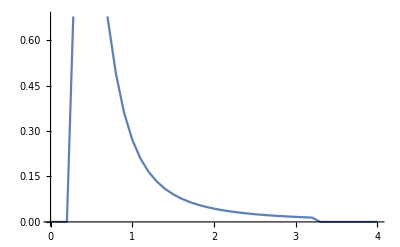

```mathematica
ListLinePlot[Table[{m,a[f0500,m]},{m,0.,4.,0.1}]]
```

ASSERTION FAILED: HoldComplete[Assert[pRatio1$15415772 > 0]]

ASSERTION FAILED: HoldComplete[Assert[pRatio$15415772 > 0]]

ASSERTION FAILED: HoldComplete[Assert[pRatio1$15419227 > 0]]

ASSERTION FAILED: HoldComplete[Assert[pRatio$15419227 > 0]]

ASSERTION FAILED: HoldComplete[Assert[pRatio1$15472692 > 0]]

ASSERTION FAILED: HoldComplete[Assert[pRatio$15472692 > 0]]

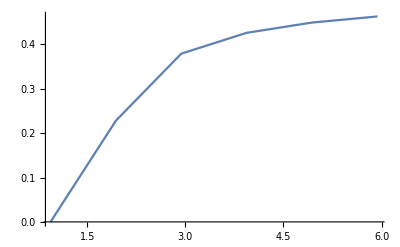

```mathematica
Monitor[
ListLinePlot[
Table[{m,Γ[N1650,m]},{m,minMass@N1650,maxMass@N1650,1.}],
PlotRange->All
],
```

```mathematica
Close[Streams[][[3]]]
```

/home/b2/marius/Documents/Pythia8/Mathematica/ParticleWidths.xml

```mathematica
Streams[]
```

{OutputStream[…],OutputStream[…]}

```mathematica
ClebschGordan[{1,0},{1,0},{0,0}]
```

-1/(√3)

```mathematica
minMass[rho]
```

0.278

```mathematica
minMass[f0500]
```

0.278

```mathematica
isMeson[f0500]
```

True

```mathematica
mMax[rho]
```

mMax[rho]

```mathematica
Streams[]
```

{OutputStream[…],OutputStream[…]}

```mathematica
Close[Streams[][[3]]]
```

/home/b2/marius/Documents/Pythia8/Mathematica/ParticleWidths.xml

```mathematica
minMass@rho
```

0.28

```mathematica
writeEverything[]
```

{N1440,N1520,N1535,N1650,N1675,N1680,N1700,N1710,N1720,D1232,D1600,D1620,D1700,D1905,D1910,D1920,D1950,L1405,L1520,L1600,L1670,L1690,L1690,L1800,L1810,L1820,L1830,L1890,L2100,L2110,S1385,S1660,S1670,S1750,S1775,S1915,S1940,S2030,X1530,X1820,rho,omega,f0980,Kstar,phi,K0star,a0980,f01370,K11270,a11260,f1,f11510,K21430,a21320,f21270,f21525,K11400,b11235,h11170,h11380,Kstar1680,rho1465}

N1440 2.41222/2.41222

N1520 1.02648/1.02648

N1535 0.406184/0.406184

N1650 0.474364/0.474364

N1675 1.49493/1.49493

N1680 1.08673/1.08673

N1700 0.648651/0.648651

N1710 1.01493/1.01493

N1720 1.48928/1.48928

D1232 1.76658/1.76658

D1600 2.37542/2.37542

D1620 1.46492/1.46492

D1700 1.57136/1.57136

D1905 3.01405/3.01405

D1910 2.40749/2.40749

D1920 1.52228/1.52228

D1950 2.27459/2.27459

L1405 0.128566/0.128566

L1520 0.123877/0.123877

L1600 1.54543/1.54543

L1670 0.113875/0.113875

L1690 0.300611/0.300611

L1690 0.300611/0.300611

L1800 1.94645/1.94645

L1810 1.67722/1.67722

L1820 0.645252/0.645252

L1830 0.800668/0.800668

L1890 0.590923/0.590923

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

L2100 1.79504/1.79504

L2110 1.52621/1.52621

S1385 0.522735/0.522735

S1660 0.815647/0.815647

S1670 0.603468/0.603468

S1750 0.48183/0.48183

S1775 3.82897/3.82897

S1915 1.04655/1.04655

S1940 1.43987/1.43987

S2030 1.77502/1.77502

X1530 0.0730892/0.0730892

X1820 0.14867/0.14867

rho 0.445459/0.445459

omega 0.00910404/0.00910404

f_0(980) 0.425117/0.425117

K* 0.120638/0.120638

phi 0.00707705/0.00707705

K*_0(1430) 0.319822/0.319822

a_0(980) 0.23479/0.23479

f_0(1370) 0.22138/0.22138

K_1(1270) 0.318411/0.318411

a_1(1260) 0.654549/0.654549

f_1(1285) 0.0306605/0.0306605

f_1(1510) 0.855081/0.855081

K_2(1430) 0.432048/0.432048

a_2 0.503342/0.503342

f_2 0.8945/0.8945

f'_2(1525) 0.225913/0.225913

K_1(1400) 0.264729/0.264729

b_1(1235) 0.270678/0.270678

h_1(1170) 0.732283/0.732283

h_1(1380) 0.480651/0.480651

K*(1680) 1.31587/1.31587

rho(1450) 0.996958/0.996958

```mathematica
Plot[Γ[eta958,m],{m,0.,3.}]
```

Throw::nocatch: Uncaught Throw[No decays found for eta958] returned to top level.

Hold[Throw[No decays found for eta958]]

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

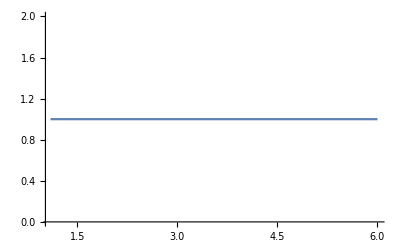

```mathematica
pts=Block[{h=D1232},
Monitor[
Table[{m,Γ[h,{N938,pi},m]/Γ[h,m]},{m,mMin[h],mMax[h],0.05}]
,m]
];
ListLinePlot[pts,PlotRange->All]
```

```mathematica
Γ[D1232,1.]
```

0

```mathematica
writeInterpolationData[$Output,pts]
```

0.00000 0.00000 0.00009 0.00471 0.02636 0.07467 0.14829 0.23603 0.32406
0.40185 0.46369 0.50787 0.53518 0.54774 0.54839 0.53846 0.52120 0.49877
0.47412 0.45000 0.42929 0.41105 0.39784 0.38873 0.38313 0.38034 0.37969
0.38057 0.38251 0.38507 0.38801 0.39109 0.39416 0.39732 0.40010 0.40250
0.40483 0.40693 0.40881 0.41048 0.41194 0.41321 0.41432 0.41528 0.41610
0.41680 0.41740 0.41924 0.41831 0.41866 0.41894 0.41916 0.41934 0.41947
0.41957 0.41963 0.41967 0.41968 0.41967 0.41964 0.41960 0.41955 0.41948
0.41940 0.41932 0.41923 0.41913 0.41903 0.41892 0.41881 0.41870 0.41859
0.41847 0.42154 0.41824 0.41812 0.41801 0.41789 0.41778 0.41766 0.41755
0.41744 0.41733 0.41722 0.41711 0.41700 0.41690 0.41680 0.41669 0.41659
0.41649 0.41640 0.41630 0.41621 0.41612 0.41602 0.42416 0.41585 0.41581
0.41568 0.41560 0.41551 0.41543 0.41536 0.41528 0.41520 0.41513 0.41506
0.41499 0.41492 0.41485 0.41478 0.41472 0.41465 0.41459 0.41453 0.41447
0.41441 0.41435 0.41429 0.41423 0.41418 0.41412 0.41407 0.41402 0.41396
0.41391 0.41386 0.41382 0.41377 0.41373 0.41367 0.41363 0.41358 0.41354
0.41350 0.41345 0.41341 0.41338 0.41333 0.41329 0.41325 0.41322 0.41318
0.41314 0.41310 0.41307 0.41303 0.41300 0.41297 0.41293

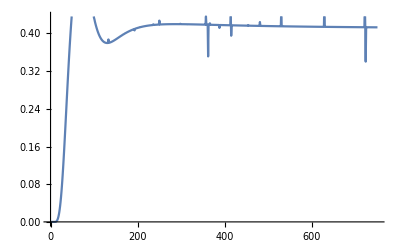

```mathematica
ListLinePlot[pts]
```

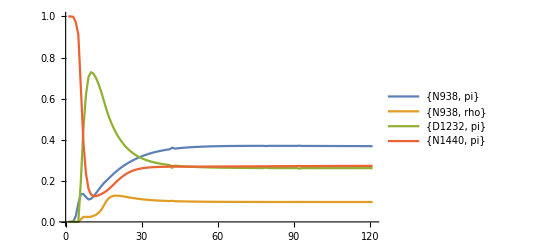

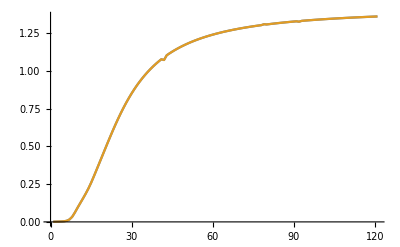

```mathematica
Module[{h,pts,gammaTotal},
h=D1700;
pts=Table[Table[Γ[h,outs,m],{m,mMin[h],mMax[h],0.05}],{outs,decayProducts[h]}];
gammaTotal=Total[pts];
pts = pts/Table[gammaTotal/.{0.->Infinity},Length[pts]];
ListLinePlot[pts,PlotRange->All,PlotLegends->ToString/@decayProducts[h]]//Print;
ListLinePlot[{gammaTotal,Table[Γ[h,m],{m,mMin[h],mMax[h],0.05}]},PlotRange->All]//Print;
]
```

```mathematica
pythiaEntries
```

{N1440,N1520,N1535,N1650,N1675,N1680,N1700,N1710,N1720,D1232,D1600,D1620,D1700,D1905,D1910,D1920,D1950 rho,omega,f0980,Ka,eta958,Kstar,phi,K0star,a0980,f01370,K11270,a11260,f1,f11510,K21430,a21320,f21270,f21525,K11400,b11235,h11170,h11380,Kstar1680,rho1465}

```mathematica
writeEverything[]
```

N1440 2.40793/2.40793

N1520 1.02581/1.02581

N1535 0.380141/0.380141

N1650 0.467144/0.467144

N1675 1.49372/1.49372

N1680 1.0863/1.0863

N1700 0.648519/0.648519

N1710 0.970628/0.970628

N1720 1.4886/1.4886

D1232 1.7627/1.7627

D1600 2.096/2.096

D1620 1.44544/1.44544

D1700 1.3597/1.3597

D1905 2.91141/2.91141

D1910 2.35931/2.35931

D1920 1.45659/1.45659

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in m near {m} = {1.41518}. NIntegrate obtained 6.35415 and 0.0000100697 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in m near {m} = {1.4238}. NIntegrate obtained 5.9163 and 0.0000488028 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in m near {m} = {569.697}. NIntegrate obtained 6.13366 and 0.000156199 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

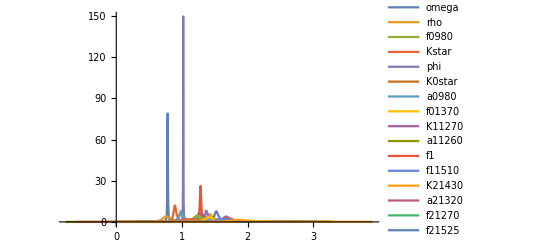

```mathematica
pts=Monitor[
Table[{h,Table[{mRes,a[h,mRes]},{mRes,m0[h]-5Γ0[h],m0[h]+5Γ0[h],0.02Γ0[h]}]},{h,Ms}],
{h,Catch@ProgressIndicator[mRes,{m0[h]-5Γ0[h],m0[h]+5Γ0[h]}]}
];
ListLinePlot[Second/@pts,PlotRange->All,PlotLegends->First/@pts]
```

```mathematica
minMass[K11270]
```

0.

```mathematica
m0@K11270
```

1.273

```mathematica
Γ0@K11270
```

0.09

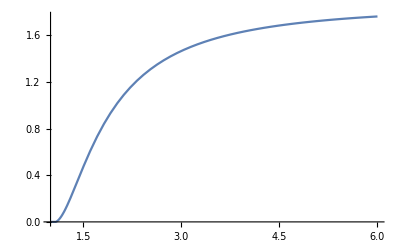

```mathematica
Plot[Γ[D1232,m],{m,1.,6}]
```

```mathematica
ListLinePlot[
Table[Γ
```